```mathematica
Get["/Users/saul/Desktop/JA_libs/QMB/Kernel/init.m"];
Get["/Users/saul/Desktop/JA_libs/QuantumWalks/Kernel/init.m"];
<<MaTeX`
```

## Rectangulo

#### Sobre la DoS, P(s) y SFF.

Dimensión del operador evolución: 1344

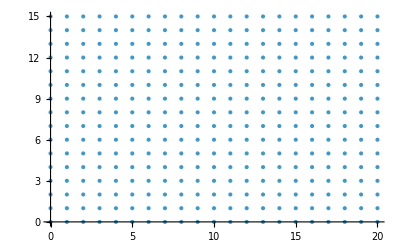

```mathematica
Lx=20;Ly=15;
GridData=GenerateRectangleBasis[Lx,Ly];
dimSpace=GridData["Dimension"];

GroverAngle=Pi/4.;
S = BuildShiftOperators[GridData, CoinDimension -> 4];
c = Coin[GeneralizedGroverCoin[Pi/4.], dimSpace];
EvolutionOp=S.c;

Print["Dimensión del operador evolución: ",EvolutionOp//Length]
ListPlot[GridData["Coords"]]
```

DoS

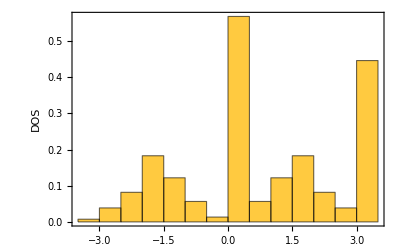

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolutionOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

Filtrando los datos

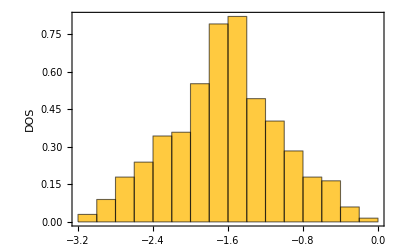

```mathematica
(* -Pi a 0 *)
FilteredPhases1= Select[eigenphases//Sort,-Pi<#<-0.001&];
Histogram[FilteredPhases1,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

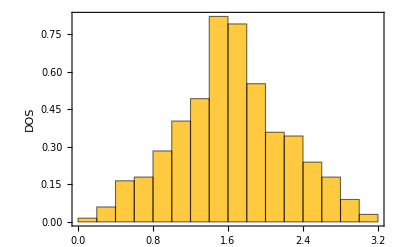

```mathematica
(* 0 a Pi *)
FilteredPhases2= Select[eigenphases//Sort,0.001<#<Pi&];
Histogram[FilteredPhases2,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

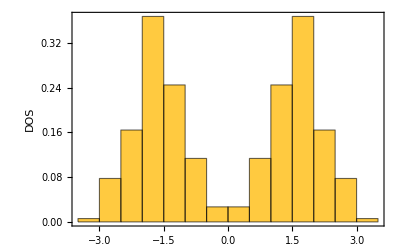

```mathematica
FilteredPhases=Join[FilteredPhases1,FilteredPhases2];
Histogram[FilteredPhases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

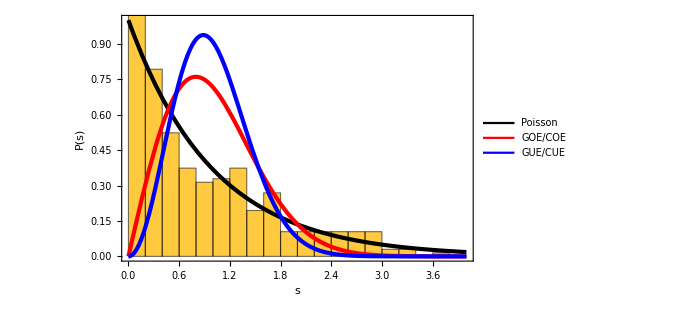

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

SFF

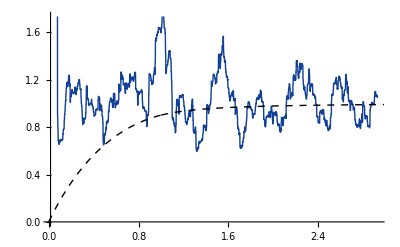

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=100;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]
]
```

## Bunimovich

#### Sobre la DoS, P(s) y SFF.

Dimensión del operador evolución: 2052

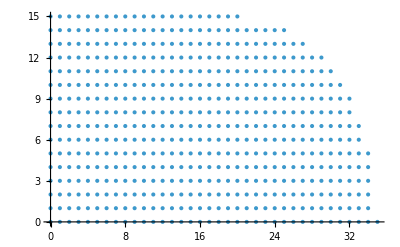

```mathematica
Lx=20;Ly=15;
GridData=GenerateBunimovichBasis[Lx,Ly];
dimSpace=GridData["Dimension"];

GroverAngle=Pi/4.;
S = BuildShiftOperators[GridData, CoinDimension -> 4];
c = Coin[GeneralizedGroverCoin[Pi/4.], dimSpace];
EvolutionOp=S.c;

Print["Dimensión del operador evolución: ",EvolutionOp//Length]
ListPlot[GridData["Coords"]]
```

DoS

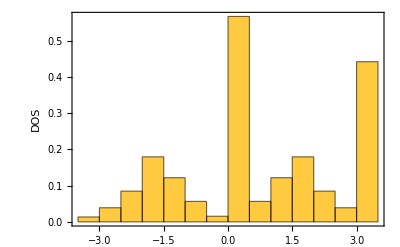

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolutionOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

Filtrando los datos

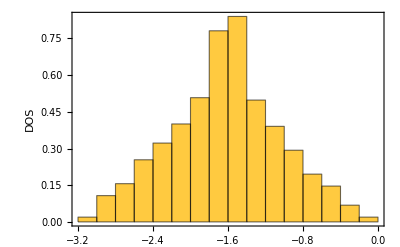

```mathematica
(* -Pi a 0 *)
FilteredPhases1= Select[eigenphases//Sort,-Pi<#<-0.001&];
Histogram[FilteredPhases1,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

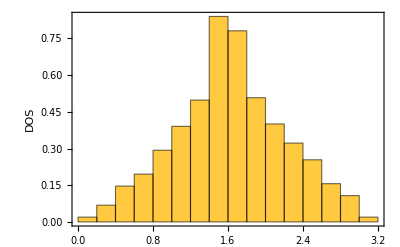

```mathematica
(* 0 a Pi *)
FilteredPhases2= Select[eigenphases//Sort,0.001<#<Pi&];
Histogram[FilteredPhases2,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

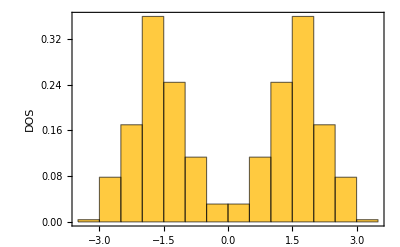

```mathematica
FilteredPhases=Join[FilteredPhases1,FilteredPhases2];
Histogram[FilteredPhases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

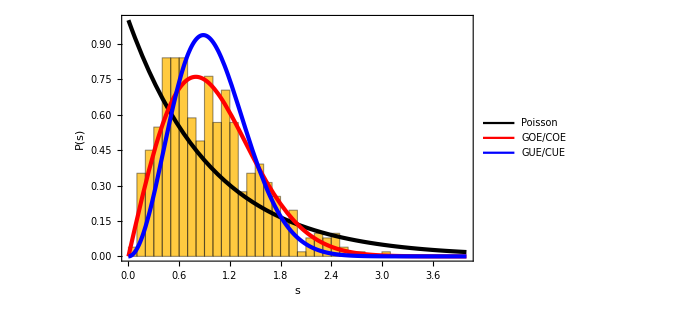

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

SFF

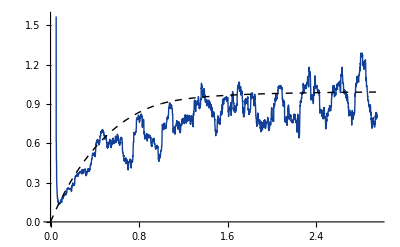

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=100;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF - Bunimovich Stadium}"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]
]
```

## Sinai

#### Sobre la DoS, P(s) y SFF.

Dimensión del operador evolución: 3796

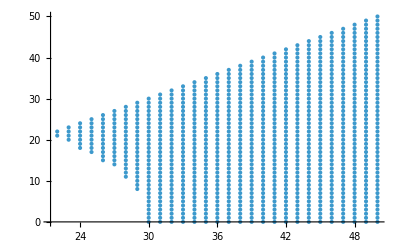

```mathematica
L1=50;R1=30;
GridData=GenerateSinaiBasis[L1,R1];
dimSpace=GridData["Dimension"];

GroverAngle=Pi/4.;
S = BuildShiftOperators[GridData, CoinDimension -> 4];
c = Coin[GeneralizedGroverCoin[Pi/4.], dimSpace];
EvolutionOp=S.c;

Print["Dimensión del operador evolución: ",EvolutionOp//Length]
ListPlot[GridData["Coords"]]
```

DoS

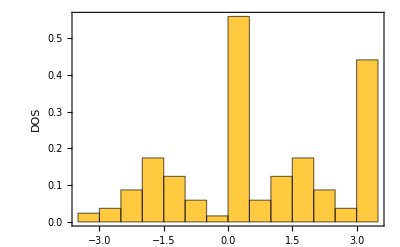

```mathematica
eigenphases = Sort[Arg[Eigenvalues[Normal[EvolutionOp]]]];
Histogram[eigenphases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

Filtrando los datos

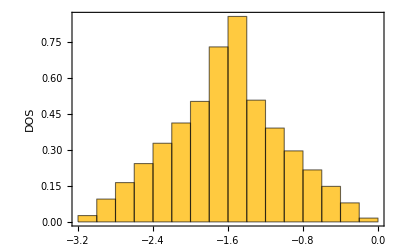

```mathematica
(* -Pi a 0 *)
FilteredPhases1= Select[eigenphases//Sort,-Pi<#<-0.001&];
Histogram[FilteredPhases1,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

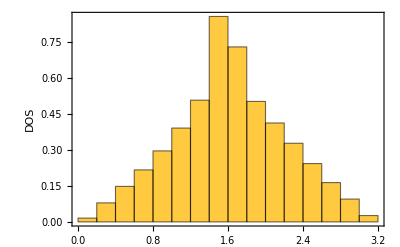

```mathematica
(* 0 a Pi *)
FilteredPhases2= Select[eigenphases//Sort,0.001<#<Pi&];
Histogram[FilteredPhases2,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

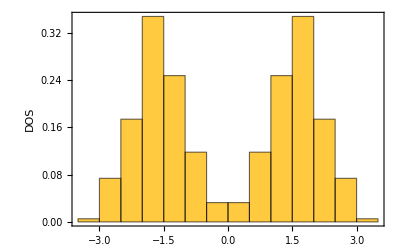

```mathematica
FilteredPhases=Join[FilteredPhases1,FilteredPhases2];
Histogram[FilteredPhases,Automatic,"PDF",PlotTheme->{"Detailed","Frame","SansLabels"},LabelStyle->18,FrameLabel->{"", "DOS"},ImageSize->400]
```

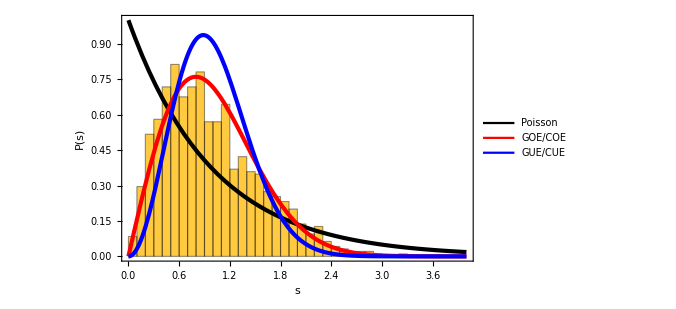

```mathematica
UnfoldedDat=Unfold[FilteredPhases//Sort]["UnfoldedLevels"];
spacings=Differences[UnfoldedDat,1];
EnsemblesList={"Poisson","GOE/COE","GUE/CUE"};
BetaValues={0,1,2};
PlotColors={Black,Red,Blue};
TheoreticalCurves=Plot[Evaluate[LevelSpacingDistribution[SVar,#]&/@BetaValues],{SVar,0,4},PlotStyle->(Directive[Thickness[0.006],#]&/@PlotColors),PlotLegends->Placed[LineLegend[PlotColors,EnsemblesList,LegendFunction->"Frame",LabelStyle->16],{0.8,0.75}]];
  EmpiricalHistogram=Histogram[spacings, "FreedmanDiaconis", "PDF",  
        PlotRange -> {{0, 4}, {0, 1}}, 
        Frame -> True, 
        FrameLabel -> {"s", "P(s)"},
        ImageSize->500,
        LabelStyle->Directive[Black, 24]];
(*6. Combine and display*)
Show[EmpiricalHistogram,TheoreticalCurves]
```

SFF

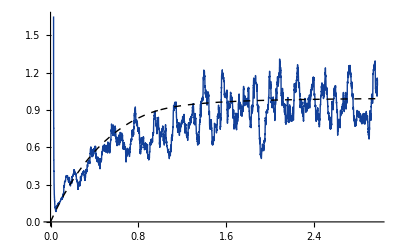

```mathematica
tmax=3;
DimSpace=Length[FilteredPhases];
TimeList=Range[1,tmax*DimSpace];
TauList=TimeList/DimSpace;

(*2. Cálculo del SFF Crudo (Normalizado)*)
SffRaw=SpectralFormFactor[FilteredPhases,TimeList]/DimSpace;

(*3. Suavizado óptimo para DTQWs (Ventana Par)*)
windowSize=100;
SffSmoothedScaled=TimeAveragedSFF[TauList,SffRaw,windowSize];

(*4. Visualización de alta calidad con MaTeX*)
Show[ListPlot[SffSmoothedScaled,PlotRange->{All,Automatic},Joined->True,PlotStyle->Directive[Thick,DarkBlue],FrameLabel->MaTeX/@{"\\tau = t/N","K(\\tau)"},PlotLabel->MaTeX["\\text{Discrete SFF }"],BaseStyle->{FontFamily->"Latin Modern Roman"}],
Plot[SpectralFormFactorRMT[τ,1],{τ,0,tmax},PlotStyle->Directive[Black,Dashed,Thick],PlotRange->{All,Automatic},PlotLegends->Placed[{MaTeX["\\text{GOE}"]},{Right,Bottom}]]
]
```

```mathematica
?GenerateFullSinaiBasis
```